```mathematica
<<Local`QFTToolKit`
QCDBaseIndices
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

VII.1 Quantizing Yang-Mills Theory

```mathematica
PR1["The Faddeev-Popov method where: ",
(tmp0={𝒵->IntegralOp[{A}, Exp[I S[A]]. Δ[A] . δ[f[A]]],
S[A]->IntegralOp[{x},ℒ],
Δ[A]->1/IntegralOp[{g},δ[f[Subscript[A, g]]]],
Subscript[A, g]->g.A.g^-1-I xPartialD[g,x].g^-1,
{g->g[x],"only function of x."}
})//Column,NL,
"Step to (4) with ",sub=f[A]->xPartialD[A,x]-σ,Yield,
tmp=tmp0[[4]]
]
```

The Faddeev-Popov method where: 𝒵→∫_A [ⅇ^(ⅈ S[A]).Δ[A].δ[f[A]]]
S[A]→∫_x [ℒ]
Δ[A]→1/(∫_g [δ[f[A_g]]])
A_g→-ⅈ UnderBar[∂]_x[g].1/g+g.A.1/g
{g→g[x],only function of x.}
Step to (4) with f[A]→-σ+UnderBar[∂]_x[A]
→ A_g→-ⅈ UnderBar[∂]_x[g].1/g+g.A.1/g

```mathematica
PR1[CO["VII.1.1. The gauge choice in the text preserves Lorentz invariance.  It is often useful to choose a gauge that breaks Lorentz invariance, for example, ", f[A]->n@u[μ]T[A,"d"][μ][x]," with n some fixed 4-vector.  This class of gauge choices, known as the axial gauge, contains various popular gauges, each of which corresponds to a particular choice of n.  For instance, in light-cone gauge, ",n->{{1,0,0,1}}," in space-cone gauge, ",n->{{0,1,I,0}},". 
Show that for any given A[x] we can find a gauge transformations so that ",n.A'[x]->0
]
]
```

VII.1.1. The gauge choice in the text preserves Lorentz invariance.  It is often useful to choose a gauge that breaks Lorentz invariance, for example, f[A]→n_μ^μ A_μ^μ[x] with n some fixed 4-vector.  This class of gauge choices, known as the axial gauge, contains various popular gauges, each of which corresponds to a particular choice of n.  For instance, in light-cone gauge, n→{{1,0,0,1}} in space-cone gauge, n→{{0,1,ⅈ,0}}. 
Show that for any given A[x] we can find a gauge transformations so that n.A'[x]→0

```mathematica
PR1["Problem: Is it is possible to find a gauge transformation, U, such that ",tmp0={T[A',"d",{μ}]->SuperDagger[U].A@d[μ].U+I SuperDagger[U].xPartialD[U,μ],
n@u[μ].T[A',"d",{μ}]->0,ForAny [n@u[μ]]},
NL,tmp=tmp0[[2]],
"POFF",

Imply,
tmpn=n@u[μ].xPartialD[U,μ]->I n@u[μ].A@d[μ].U,NL,
"Define relative distance to x in direction n: ",subλ=λ[x]->r.x/(n.r),yield,
x->λ[x].n+x@d["⊥"]," so that ",r.x@d["⊥"]->0,yield,
subλdμ=Map[xPartialD[#,μ]&,subλ],yield,
subλdμ=(subλdμ//DerivativeExpand[{r,n}])//.simpleDot2[{}] ,yield,
subλdμ=subλdμ/.r . xPartialD[x,a_]->rd[a],NL,
"Show that ",
tmp=tmp0=U[x]->Exp[I IntegralOp[{{σ,0,λ[x]}},n.A[σ.n+xd["⊥"]]]]," is such a gauge transformation that satisfies ",
tmpn, Yield,
tmp=Map[xPartialD[#,μ]&,tmp],Yield,"POFF",
tmp=tmp//DerivativeExpand[{}],Yield,
tmp=tmp/.xPartialD[IntegralOp[{{a_,a0_,a1_}},b_],c_]:>IntegralOp[{{a,a0,a1}},xPartialD[b,c]]-((b xPartialD[a0,c])/.a->a0)+((b xPartialD[a1,c])/.a->a1) ,Yield,
tmp=tmp//DerivativeExpand[{n}],NL,"PON",
tmp=tmp/.simpleDot2[{}]/.IntegralOp[_,0]->0,NL,
"Evaluate: ",
sub0=ExtractPattern[tmp,xPartialD[A[_],_]][[1]],yield,
sub=sub0/.xPartialD[A[a_],x_]->A'[a]xPartialD[a,x],yield,
sub=sub0->(sub//DerivativeExpand[{n,σ}])/.simpleDot2[{}],yield,
sub=sub/.xPartialD[xd["⊥"],a_]->nd["⊥"],NL,
"Taking Dot with n: ",Yield,
tmp=Map[nu[μ ].#&,(tmp/.sub)],Yield,
tmp=(tmp//DerivativeExpand[{n,σ}])//.simpleDot2[{Dot[a_,b_],IntegralOp[__],Exp[_],nd["⊥"]}]//.IntegralOp[a_,b_ nd["⊥"]]->nd["⊥"]IntegralOp[a,b]/.subλdμ,NL,"Since ",
sub={nd["⊥"]nu[μ]->0,nu[μ]rd[μ]->n.r},Imply,
tmp=tmp/.sub/.Reverse[tmp0]," QED"
];
```

Problem: Is it is possible to find a gauge transformation, U, such that {A'_μ^μ→ⅈ U^†.UnderBar[∂]_μ[U]+U^†.A_μ^μ.U,n_μ^μ.A'_μ^μ→0,ForAny[n_μ^μ]}
n_μ^μ.A'_μ^μ→0UnderBar[∂]_μ[U[x]]→ⅈ ⅇ^(ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+xd[⊥]]]) (∫_{σ,0,λ[x]} [n.UnderBar[∂]_μ[A[σ.n+xd[⊥]]]]+n.A[λ[x].n+xd[⊥]] UnderBar[∂]_μ[λ[x]])
Evaluate: UnderBar[∂]_μ[A[σ.n+xd[⊥]]] ⟶ UnderBar[∂]_μ[σ.n+xd[⊥]] A'[σ.n+xd[⊥]] ⟶ UnderBar[∂]_μ[A[σ.n+xd[⊥]]]→UnderBar[∂]_μ[xd[⊥]] A'[σ.n+xd[⊥]] ⟶ UnderBar[∂]_μ[A[σ.n+xd[⊥]]]→nd[⊥] A'[σ.n+xd[⊥]]
Taking Dot with n: 
→ nu[μ].UnderBar[∂]_μ[U[x]]→nu[μ].(ⅈ ⅇ^(ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+xd[⊥]]]) (∫_{σ,0,λ[x]} [n.(nd[⊥] A'[σ.n+xd[⊥]])]+n.A[λ[x].n+xd[⊥]] UnderBar[∂]_μ[λ[x]]))
→ nu[μ].UnderBar[∂]_μ[U[x]]→ⅇ^(ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+xd[⊥]]]) (ⅈ n.A[λ[x].n+xd[⊥]] nu[μ].rd[μ]/(n.r)+ⅈ ∫_{σ,0,λ[x]} [n.A'[σ.n+xd[⊥]]] nd[⊥] nu[μ])
Since {nd[⊥] nu[μ]→0,nu[μ] rd[μ]→n.r}
⇒ nu[μ].UnderBar[∂]_μ[U[x]]→ⅈ n.A[λ[x].n+xd[⊥]] nu[μ].rd[μ]/(n.r) U[x] QED

```mathematica
PR1[CO["VII.1.2. Derive (17) and relate f to the coupling g in the continuum formulation of Yang-Mills theory."],
NL,"Use the Baker-Campbell-Hausdorff formula: ",
subBCH=Exp[A_].Exp[B_]->Exp[A+B+Com[A,B]/2+(Com[A,Com[A,B]]+Com[B,Com[B,A]])/12],Imply,
"(17) is ",
(tmp0={
e17=Tr[Udd[i,j]. Udd[j,k]. Udd[k,l]. Udd[l,i]]->Tr[Exp[I a^2 Fdd[μ,ν]+xO[a^3]]],
Udd[i_,j_]->SuperDagger[Vd[i]].Exp[I a Ad[μ[i,j]][x]].Vd[j]
})//Column,Yield,
tmp=tmp0[[1]]/.tmp0[[2]],NL,
"Eliminate V's by using cyclic property of Tr and unitarity of V's",Yield,
tmp0=tmp/. SuperDagger[a_] . b__ . a_->b.a.SuperDagger[a]//.a_ .SuperDagger[a_]->1//.simpleDot2[{}]
];
```

Derive (17) and relate f to the coupling g in the continuum formulation of Yang-Mills theory.  Use the Baker-Campbell-Hausdorff formula: ⅇ^A_.ⅇ^B_→ⅇ^(A+B+1/2 Com[A,B]+1/12 (Com[A,Com[A,B]]+Com[B,Com[B,A]]))
⇒ (17) is Tr[U_ij^ij.U_jk^jk.U_kl^kl.U_li^li]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xO[a^3])]
U_i_j_^i_j_→(V_i^i)^†.ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).V_j^j
→ Tr[(V_i^i)^†.ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).V_j^j.(V_j^j)^†.ⅇ^(ⅈ a A_μ[j,k]^μ[j,k][x]).V_k^k.(V_k^k)^†.ⅇ^(ⅈ a A_μ[k,l]^μ[k,l][x]).V_l^l.(V_l^l)^†.ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][x]).V_i^i]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xO[a^3])]
Eliminate V's by using cyclic property of Tr and unitarity of V's
→ Tr[ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).ⅇ^(ⅈ a A_μ[j,k]^μ[j,k][x]).ⅇ^(ⅈ a A_μ[k,l]^μ[k,l][x]).ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][x])]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xO[a^3])]

```mathematica
PR1["Verify the Baker-Campbell-Hausdorff formula ",
tmp=subBCH//RemovePatterns,Yield,
tmp=tmp/.Exp[a_]->Exp[x a]/.Rule->Equal,Yield,
tmp=tmp//.Exp[a_]:>Series[Exp[a],{x,0,3}]//Normal,Yield,
tmp=tmp/.x->1/.Power[a_,2]->a.a/.Power[a_,3]->a.a.a/.Com->MCommutator,Yield,
tmp=tmp//.simpleDot2[{}]//Simplify;NL,
"OK to O[3], the O[4] difference equation: ",Yield,
tmp=tmp//.{A-> x xA,B->x xB}//.simpleDot2[{x}]//Simplify;
tmp=Collect[tmp,x,Simplify];
tmp=tmp/.x^n_:>0/;n>4//.{xA->A,xB->B,x->1}
]
```

Verify the Baker-Campbell-Hausdorff formula ⅇ^A.ⅇ^B→ⅇ^(A+B+1/2 Com[A,B]+1/12 (Com[A,Com[A,B]]+Com[B,Com[B,A]]))
→ ⅇ^(A x).ⅇ^(B x)==ⅇ^(x (A+B+1/2 Com[A,B]+1/12 (Com[A,Com[A,B]]+Com[B,Com[B,A]])))
→ (1+A x+(A^2 x^2)/2+(A^3 x^3)/6).(1+B x+(B^2 x^2)/2+(B^3 x^3)/6)==1+1/12 x (12 A+12 B+6 Com[A,B]+Com[A,Com[A,B]]+Com[B,Com[B,A]])+1/288 x^2 (12 A+12 B+6 Com[A,B]+Com[A,Com[A,B]]+Com[B,Com[B,A]])^2+(x^3 (12 A+12 B+6 Com[A,B]+Com[A,Com[A,B]]+Com[B,Com[B,A]])^3)/10368
→ (1+A+(A.A)/2+(A.A.A)/6).(1+B+(B.B)/2+(B.B.B)/6)==1+1/12 (12 A+12 B+A.(A.B-B.A)+6 (A.B-B.A)+B.(-A.B+B.A)-(A.B-B.A).A-(-A.B+B.A).B)+1/288 (12 A+12 B+A.(A.B-B.A)+6 (A.B-B.A)+B.(-A.B+B.A)-(A.B-B.A).A-(-A.B+B.A).B).(12 A+12 B+A.(A.B-B.A)+6 (A.B-B.A)+B.(-A.B+B.A)-(A.B-B.A).A-(-A.B+B.A).B)+1/10368(12 A+12 B+A.(A.B-B.A)+6 (A.B-B.A)+B.(-A.B+B.A)-(A.B-B.A).A-(-A.B+B.A).B).(12 A+12 B+A.(A.B-B.A)+6 (A.B-B.A)+B.(-A.B+B.A)-(A.B-B.A).A-(-A.B+B.A).B).(12 A+12 B+A.(A.B-B.A)+6 (A.B-B.A)+B.(-A.B+B.A)-(A.B-B.A).A-(-A.B+B.A).B)
→ 2 (216 A.A.A.B+216 A.A.B.A+432 A.A.B.B+216 A.B.A.A+216 A.B.B.A+216 A.B.B.B+216 B.A.A.A+216 B.A.A.B+648 B.A.B.A+216 B.A.B.B+216 B.B.A.B+216 B.B.B.A+72 A.A.A.B.A+288 A.A.A.B.B+108 A.A.B.B.A+288 A.A.B.B.B+72 A.B.A.A.A+108 A.B.A.A.B+216 A.B.A.B.A+108 A.B.B.A.B+72 A.B.B.B.A+72 B.A.A.A.B+108 B.A.A.B.B+108 B.A.B.A.A+216 B.A.B.A.B+72 B.A.B.B.B+108 B.B.A.B.A+72 B.B.B.A.B+36 A.A.A.B.B.A+144 A.A.A.B.B.B+36 A.A.B.A.B.A+72 A.A.B.B.A.B+18 A.A.B.B.B.A+72 A.B.A.A.A.B+72 A.B.A.A.B.B+36 A.B.A.B.A.A+108 A.B.B.A.B.A+72 A.B.B.B.A.B+18 B.A.A.A.B.B+18 B.A.A.B.B.A+36 B.A.A.B.B.B+36 B.A.B.A.A.A+108 B.A.B.A.A.B+36 B.A.B.A.B.B+54 B.B.A.B.A.A+36 B.B.A.B.A.B+36 B.B.B.A.B.A+12 A.A.A.B.A.B.A+12 A.A.A.B.B.A.B+6 A.A.B.A.A.A.B+18 A.A.B.A.B.A.A+18 A.A.B.A.B.B.A+18 A.A.B.B.A.B.A+18 A.A.B.B.B.A.B+6 A.B.A.A.A.A.B+18 A.B.A.A.A.B.B+12 A.B.A.A.B.B.B+12 A.B.A.B.A.A.A+18 A.B.A.B.A.A.B+18 A.B.A.B.B.A.A+24 A.B.A.B.B.B.A+18 A.B.B.A.B.A.A+18 A.B.B.A.B.A.B+24 A.B.B.B.A.B.A+6 A.B.B.B.A.B.B+6 A.B.B.B.B.A.B+6 B.A.A.A.A.B.A+6 B.A.A.A.B.A.A+24 B.A.A.A.B.A.B+18 B.A.A.B.A.B.A+18 B.A.A.B.A.B.B+24 B.A.B.A.A.A.B+18 B.A.B.A.A.B.B+18 B.A.B.A.B.B.A+12 B.A.B.A.B.B.B+12 B.A.B.B.A.A.A+18 B.A.B.B.B.A.A+6 B.A.B.B.B.B.A+18 B.B.A.A.A.B.A+18 B.B.A.A.B.A.B+18 B.B.A.B.A.A.B+18 B.B.A.B.A.B.B+6 B.B.A.B.B.B.A+12 B.B.B.A.A.B.A+12 B.B.B.A.B.A.B+3 A.A.B.A.A.B.B.A+3 A.A.B.A.B.A.A.B+3 A.A.B.A.B.B.A.B+3 A.A.B.B.A.A.B.B+3 A.A.B.B.A.B.A.A+3 A.A.B.B.B.A.B.A+6 A.B.A.A.A.B.A.B+6 A.B.A.A.B.A.B.A+3 A.B.A.A.B.A.B.B+3 A.B.A.A.B.B.A.A+6 A.B.A.B.A.A.A.B+12 A.B.A.B.A.B.B.A+3 A.B.A.B.B.A.A.B+6 A.B.A.B.B.B.A.B+6 A.B.B.A.A.A.B.A+3 A.B.B.A.A.B.A.B+9 A.B.B.A.B.A.A.B+3 A.B.B.A.B.A.B.B+3 A.B.B.A.B.B.A.A+6 A.B.B.A.B.B.B.A+3 A.B.B.B.A.A.B.A+6 A.B.B.B.A.B.A.B+3 A.B.B.B.B.A.B.A+3 B.A.A.A.A.B.B.A+6 B.A.A.A.B.A.A.B+3 B.A.A.A.B.B.B.A+9 B.A.A.B.A.A.B.A+12 B.A.A.B.A.B.A.B+3 B.A.A.B.B.A.B.B+3 B.A.A.B.B.B.A.A+3 B.A.A.B.B.B.B.A+3 B.A.B.A.A.A.A.B+3 B.A.B.A.A.A.B.B+3 B.A.B.A.A.B.A.A+12 B.A.B.A.B.A.B.A+6 B.A.B.A.B.B.A.B+3 B.A.B.B.A.A.A.B+9 B.A.B.B.A.B.B.A+6 B.A.B.B.B.A.A.B+3 B.B.A.A.A.B.B.A+3 B.B.A.A.B.A.A.B+3 B.B.A.A.B.B.A.B+3 B.B.A.B.A.A.B.B+3 B.B.A.B.A.B.A.A+3 B.B.A.B.B.A.B.A+A.A.B.A.A.B.A.B.A+A.A.B.A.A.B.B.A.B+A.A.B.A.B.A.A.A.B+A.A.B.A.B.A.A.B.B+A.A.B.A.B.A.B.A.A+A.A.B.A.B.A.B.B.A+A.A.B.A.B.B.A.B.A+A.A.B.A.B.B.B.A.B+A.A.B.B.A.A.A.B.A+A.A.B.B.A.A.B.A.B+A.A.B.B.A.B.A.A.B+A.A.B.B.A.B.A.B.B+A.A.B.B.A.B.B.A.A+A.A.B.B.A.B.B.B.A+A.A.B.B.B.A.A.B.A+A.A.B.B.B.A.B.A.B+A.B.A.A.A.B.A.A.B+A.B.A.A.A.B.A.B.B+A.B.A.A.A.B.B.A.A+A.B.A.A.A.B.B.B.A+4 A.B.A.A.B.A.A.B.A+4 A.B.A.A.B.A.B.A.B+A.B.A.A.B.B.A.A.B+A.B.A.A.B.B.A.B.B+A.B.A.A.B.B.B.A.A+A.B.A.A.B.B.B.B.A+A.B.A.B.A.A.A.A.B+A.B.A.B.A.A.A.B.B+A.B.A.B.A.A.B.A.A+A.B.A.B.A.A.B.B.A+4 A.B.A.B.A.B.A.B.A+4 A.B.A.B.A.B.B.A.B+A.B.A.B.B.A.A.A.B+A.B.A.B.B.A.A.B.B+A.B.A.B.B.A.B.A.A+A.B.A.B.B.A.B.B.A+A.B.B.A.A.B.A.B.A+A.B.B.A.A.B.B.A.B+A.B.B.A.B.A.A.A.B+A.B.B.A.B.A.A.B.B+A.B.B.A.B.A.B.A.A+A.B.B.A.B.A.B.B.A+A.B.B.A.B.B.A.B.A+A.B.B.A.B.B.B.A.B+A.B.B.B.A.A.A.B.A+A.B.B.B.A.A.B.A.B+A.B.B.B.A.B.A.A.B+A.B.B.B.A.B.A.B.B+A.B.B.B.A.B.B.A.A+A.B.B.B.A.B.B.B.A+A.B.B.B.B.A.A.B.A+A.B.B.B.B.A.B.A.B+B.A.A.A.A.B.A.B.A+B.A.A.A.A.B.B.A.B+B.A.A.A.B.A.A.A.B+B.A.A.A.B.A.A.B.B+B.A.A.A.B.A.B.A.A+B.A.A.A.B.A.B.B.A+B.A.A.A.B.B.A.B.A+B.A.A.A.B.B.B.A.B+B.A.A.B.A.A.A.B.A+B.A.A.B.A.A.B.A.B+B.A.A.B.A.B.A.A.B+B.A.A.B.A.B.A.B.B+B.A.A.B.A.B.B.A.A+B.A.A.B.A.B.B.B.A+B.A.A.B.B.A.A.B.A+B.A.A.B.B.A.B.A.B+B.A.B.A.A.B.A.A.B+B.A.B.A.A.B.A.B.B+B.A.B.A.A.B.B.A.A+B.A.B.A.A.B.B.B.A+4 B.A.B.A.B.A.A.B.A+4 B.A.B.A.B.A.B.A.B+B.A.B.A.B.B.A.A.B+B.A.B.A.B.B.A.B.B+B.A.B.A.B.B.B.A.A+B.A.B.A.B.B.B.B.A+B.A.B.B.A.A.A.A.B+B.A.B.B.A.A.A.B.B+B.A.B.B.A.A.B.A.A+B.A.B.B.A.A.B.B.A+4 B.A.B.B.A.B.A.B.A+4 B.A.B.B.A.B.B.A.B+B.A.B.B.B.A.A.A.B+B.A.B.B.B.A.A.B.B+B.A.B.B.B.A.B.A.A+B.A.B.B.B.A.B.B.A+B.B.A.A.A.B.A.B.A+B.B.A.A.A.B.B.A.B+B.B.A.A.B.A.A.A.B+B.B.A.A.B.A.A.B.B+B.B.A.A.B.A.B.A.A+B.B.A.A.B.A.B.B.A+B.B.A.A.B.B.A.B.A+B.B.A.A.B.B.B.A.B+B.B.A.B.A.A.A.B.A+B.B.A.B.A.A.B.A.B+B.B.A.B.A.B.A.A.B+B.B.A.B.A.B.A.B.B+B.B.A.B.A.B.B.A.A+B.B.A.B.A.B.B.B.A+B.B.A.B.B.A.A.B.A+B.B.A.B.B.A.B.A.B)==432 A.B.A.B+144 A.A.A.A.B+216 A.A.B.A.B+216 A.B.A.B.B+216 A.B.B.A.A+144 A.B.B.B.B+144 B.A.A.A.A+216 B.A.A.B.A+216 B.A.B.B.A+288 B.B.A.A.A+216 B.B.A.A.B+288 B.B.B.A.A+144 B.B.B.B.A+72 A.A.A.B.A.B+36 A.A.B.A.A.B+180 A.A.B.A.B.B+36 A.A.B.B.A.A+144 A.B.A.A.B.A+72 A.B.A.B.A.B+72 A.B.A.B.B.A+72 A.B.A.B.B.B+72 A.B.B.A.A.A+108 A.B.B.A.A.B+36 A.B.B.A.B.B+108 A.B.B.B.A.A+36 A.B.B.B.B.A+36 B.A.A.A.A.B+36 B.A.A.B.A.A+72 B.A.A.B.A.B+216 B.A.B.A.B.A+144 B.A.B.B.A.B+108 B.B.A.A.A.B+36 B.B.A.A.B.B+36 B.B.A.B.B.A+72 B.B.B.A.A.B+12 A.A.A.B.A.A.B+12 A.A.A.B.A.B.B+12 A.A.A.B.B.A.A+12 A.A.A.B.B.B.A+36 A.A.B.A.A.B.A+36 A.A.B.A.B.A.B+12 A.A.B.A.B.B.B+12 A.A.B.B.A.A.A+36 A.A.B.B.B.A.A+24 A.A.B.B.B.B.A+36 A.B.A.A.B.A.A+36 A.B.A.A.B.A.B+72 A.B.A.B.A.B.A+36 A.B.A.B.A.B.B+36 A.B.A.B.B.A.B+24 A.B.B.A.A.A.B+36 A.B.B.A.B.B.A+12 A.B.B.A.B.B.B+12 A.B.B.B.A.A.A+24 A.B.B.B.A.A.B+24 A.B.B.B.B.A.A+12 A.B.B.B.B.B.A+12 B.A.A.A.A.A.B+24 B.A.A.A.A.B.B+24 B.A.A.A.B.B.A+12 B.A.A.A.B.B.B+12 B.A.A.B.A.A.A+36 B.A.A.B.A.A.B+24 B.A.A.B.B.B.A+36 B.A.B.A.A.B.A+36 B.A.B.A.B.A.A+72 B.A.B.A.B.A.B+36 B.A.B.B.A.B.A+36 B.A.B.B.A.B.B+24 B.B.A.A.A.A.B+36 B.B.A.A.A.B.B+12 B.B.A.A.B.B.B+12 B.B.A.B.A.A.A+36 B.B.A.B.A.B.A+36 B.B.A.B.B.A.B+12 B.B.B.A.A.A.B+12 B.B.B.A.A.B.B+12 B.B.B.A.B.A.A+12 B.B.B.A.B.B.A+6 A.A.B.A.A.B.A.B+6 A.A.B.A.B.A.B.B+6 A.A.B.A.B.B.A.A+6 A.A.B.B.A.A.B.A+6 A.A.B.B.A.B.B.A+6 A.A.B.B.B.A.A.B+12 A.B.A.A.A.B.B.A+18 A.B.A.A.B.A.A.B+6 A.B.A.A.B.B.B.A+12 A.B.A.B.A.A.B.A+24 A.B.A.B.A.B.A.B+6 A.B.A.B.B.A.B.B+6 A.B.A.B.B.B.A.A+6 A.B.A.B.B.B.B.A+6 A.B.B.A.A.A.A.B+6 A.B.B.A.A.A.B.B+6 A.B.B.A.A.B.A.A+24 A.B.B.A.B.A.B.A+18 A.B.B.A.B.B.A.B+6 A.B.B.B.A.A.A.B+12 A.B.B.B.A.B.B.A+6 A.B.B.B.B.A.A.B+6 B.A.A.A.A.B.A.B+12 B.A.A.A.B.A.B.A+6 B.A.A.A.B.B.A.B+12 B.A.A.B.A.A.A.B+6 B.A.A.B.A.A.B.B+6 B.A.A.B.A.B.A.A+18 B.A.A.B.A.B.B.A+6 B.A.A.B.B.A.B.A+12 B.A.A.B.B.B.A.B+12 B.A.B.A.A.A.B.A+6 B.A.B.A.A.B.B.A+24 B.A.B.A.B.A.A.B+12 B.A.B.A.B.B.B.A+6 B.A.B.B.A.A.B.B+6 B.A.B.B.A.B.A.A+12 B.A.B.B.A.B.A.B+12 B.A.B.B.B.A.B.A+6 B.B.A.A.A.B.A.B+6 B.B.A.A.B.A.B.B+6 B.B.A.A.B.B.A.A+6 B.B.A.B.A.A.B.A+6 B.B.A.B.A.B.B.A+6 B.B.A.B.B.A.A.B+A.A.B.A.A.B.A.A.B+A.A.B.A.A.B.A.B.B+A.A.B.A.A.B.B.A.A+A.A.B.A.A.B.B.B.A+4 A.A.B.A.B.A.A.B.A+4 A.A.B.A.B.A.B.A.B+A.A.B.A.B.B.A.A.B+A.A.B.A.B.B.A.B.B+A.A.B.A.B.B.B.A.A+A.A.B.A.B.B.B.B.A+A.A.B.B.A.A.A.A.B+A.A.B.B.A.A.A.B.B+A.A.B.B.A.A.B.A.A+A.A.B.B.A.A.B.B.A+4 A.A.B.B.A.B.A.B.A+4 A.A.B.B.A.B.B.A.B+A.A.B.B.B.A.A.A.B+A.A.B.B.B.A.A.B.B+A.A.B.B.B.A.B.A.A+A.A.B.B.B.A.B.B.A+4 A.B.A.A.A.B.A.B.A+4 A.B.A.A.A.B.B.A.B+4 A.B.A.A.B.A.A.A.B+4 A.B.A.A.B.A.A.B.B+4 A.B.A.A.B.A.B.A.A+4 A.B.A.A.B.A.B.B.A+4 A.B.A.A.B.B.A.B.A+4 A.B.A.A.B.B.B.A.B+4 A.B.A.B.A.A.A.B.A+4 A.B.A.B.A.A.B.A.B+4 A.B.A.B.A.B.A.A.B+4 A.B.A.B.A.B.A.B.B+4 A.B.A.B.A.B.B.A.A+4 A.B.A.B.A.B.B.B.A+4 A.B.A.B.B.A.A.B.A+4 A.B.A.B.B.A.B.A.B+A.B.B.A.A.B.A.A.B+A.B.B.A.A.B.A.B.B+A.B.B.A.A.B.B.A.A+A.B.B.A.A.B.B.B.A+4 A.B.B.A.B.A.A.B.A+4 A.B.B.A.B.A.B.A.B+A.B.B.A.B.B.A.A.B+A.B.B.A.B.B.A.B.B+A.B.B.A.B.B.B.A.A+A.B.B.A.B.B.B.B.A+A.B.B.B.A.A.A.A.B+A.B.B.B.A.A.A.B.B+A.B.B.B.A.A.B.A.A+A.B.B.B.A.A.B.B.A+4 A.B.B.B.A.B.A.B.A+4 A.B.B.B.A.B.B.A.B+A.B.B.B.B.A.A.A.B+A.B.B.B.B.A.A.B.B+A.B.B.B.B.A.B.A.A+A.B.B.B.B.A.B.B.A+B.A.A.A.A.B.A.A.B+B.A.A.A.A.B.A.B.B+B.A.A.A.A.B.B.A.A+B.A.A.A.A.B.B.B.A+4 B.A.A.A.B.A.A.B.A+4 B.A.A.A.B.A.B.A.B+B.A.A.A.B.B.A.A.B+B.A.A.A.B.B.A.B.B+B.A.A.A.B.B.B.A.A+B.A.A.A.B.B.B.B.A+B.A.A.B.A.A.A.A.B+B.A.A.B.A.A.A.B.B+B.A.A.B.A.A.B.A.A+B.A.A.B.A.A.B.B.A+4 B.A.A.B.A.B.A.B.A+4 B.A.A.B.A.B.B.A.B+B.A.A.B.B.A.A.A.B+B.A.A.B.B.A.A.B.B+B.A.A.B.B.A.B.A.A+B.A.A.B.B.A.B.B.A+4 B.A.B.A.A.B.A.B.A+4 B.A.B.A.A.B.B.A.B+4 B.A.B.A.B.A.A.A.B+4 B.A.B.A.B.A.A.B.B+4 B.A.B.A.B.A.B.A.A+4 B.A.B.A.B.A.B.B.A+4 B.A.B.A.B.B.A.B.A+4 B.A.B.A.B.B.B.A.B+4 B.A.B.B.A.A.A.B.A+4 B.A.B.B.A.A.B.A.B+4 B.A.B.B.A.B.A.A.B+4 B.A.B.B.A.B.A.B.B+4 B.A.B.B.A.B.B.A.A+4 B.A.B.B.A.B.B.B.A+4 B.A.B.B.B.A.A.B.A+4 B.A.B.B.B.A.B.A.B+B.B.A.A.A.B.A.A.B+B.B.A.A.A.B.A.B.B+B.B.A.A.A.B.B.A.A+B.B.A.A.A.B.B.B.A+4 B.B.A.A.B.A.A.B.A+4 B.B.A.A.B.A.B.A.B+B.B.A.A.B.B.A.A.B+B.B.A.A.B.B.A.B.B+B.B.A.A.B.B.B.A.A+B.B.A.A.B.B.B.B.A+B.B.A.B.A.A.A.A.B+B.B.A.B.A.A.A.B.B+B.B.A.B.A.A.B.A.A+B.B.A.B.A.A.B.B.A+4 B.B.A.B.A.B.A.B.A+4 B.B.A.B.A.B.B.A.B+B.B.A.B.B.A.A.A.B+B.B.A.B.B.A.A.B.B+B.B.A.B.B.A.B.A.A+B.B.A.B.B.A.B.B.A
OK to O[3], the O[4] equation: 
→ 432 (A.A.A.B+A.A.B.A+2 A.A.B.B+A.B.A.A+A.B.B.A+A.B.B.B+B.A.A.A+B.A.A.B+3 B.A.B.A+B.A.B.B+B.B.A.B+B.B.B.A)==432 A.B.A.B

```mathematica
PR1["Linear estimate of ",tmpA=Ad[μ][x]," about center of plaque in at {i,j} and μ[i,j] indicates A in direction perpendicular to ",xdd[i,j]," since the U is transformation along the {ij} axis",yield,
tmp=Normal[Series[tmpA,{x,0,1}]]/.{A_'->xPartialD[A,{x}]};
(*and unclutter notation*)
subA=tmpA->tmp/.x->xdd[i,j]/.μ->μ[i,j]/.a_[0]->a,NL,
"For the other sides ",
(subA1={subA,
subAjk=subA/.{j->k,i->j},
subAkl=subA/.{i->k,j->l},
subAli=subA/.{i->l,j->i}
})//Column,NL,
"For a^2 plaque ",sub={xPartialD[A_,{xdd[i_,j_]}]->xPartialD[A,{pdd[i,j]}],
xdd[i,j]->-a/2,xdd[j,k]->a/2,xdd[k,l]->a/2,xdd[l,i]->-a/2},Yield,
(subA2=Map[MapAt[#/.sub&,#,2]&,subA1])//Column,
" where ",pdd[i,j]," is perpendicular to ",μdd[i,j]
]
```

Linear estimate of A_μ^μ[x] about center of plaque in at {i,j} and μ[i,j] indicates A in direction perpendicular to x_ij^ij since the U is transformation along the {ij} axis ⟶ A_μ[i,j]^μ[i,j][x_ij^ij]→A_μ[i,j]^μ[i,j]+x_ij^ij UnderBar[∂]_{x_ij^ij}[A_μ[i,j]^μ[i,j]]
For the other sides A_μ[i,j]^μ[i,j][x_ij^ij]→A_μ[i,j]^μ[i,j]+x_ij^ij UnderBar[∂]_{x_ij^ij}[A_μ[i,j]^μ[i,j]]
A_μ[j,k]^μ[j,k][x_jk^jk]→A_μ[j,k]^μ[j,k]+x_jk^jk UnderBar[∂]_{x_jk^jk}[A_μ[j,k]^μ[j,k]]
A_μ[k,l]^μ[k,l][x_kl^kl]→A_μ[k,l]^μ[k,l]+x_kl^kl UnderBar[∂]_{x_kl^kl}[A_μ[k,l]^μ[k,l]]
A_μ[l,i]^μ[l,i][x_li^li]→A_μ[l,i]^μ[l,i]+x_li^li UnderBar[∂]_{x_li^li}[A_μ[l,i]^μ[l,i]]
For a^2 plaque {UnderBar[∂]_{x_i_j_^i_j_}[A_]→UnderBar[∂]_{p_ij^ij}[A],x_ij^ij→-a/2,x_jk^jk→a/2,x_kl^kl→a/2,x_li^li→-a/2}
→ A_μ[i,j]^μ[i,j][x_ij^ij]→A_μ[i,j]^μ[i,j]-1/2 a UnderBar[∂]_{p_ij^ij}[A_μ[i,j]^μ[i,j]]
A_μ[j,k]^μ[j,k][x_jk^jk]→A_μ[j,k]^μ[j,k]+1/2 a UnderBar[∂]_{p_jk^jk}[A_μ[j,k]^μ[j,k]]
A_μ[k,l]^μ[k,l][x_kl^kl]→A_μ[k,l]^μ[k,l]+1/2 a UnderBar[∂]_{p_kl^kl}[A_μ[k,l]^μ[k,l]]
A_μ[l,i]^μ[l,i][x_li^li]→A_μ[l,i]^μ[l,i]-1/2 a UnderBar[∂]_{p_li^li}[A_μ[l,i]^μ[l,i]] where p_ij^ij is perpendicular to μdd[i,j]

```mathematica
PR1["Examine ",tmp=tmp0[[1,1]],Yield,
tmp=tmp/.(subA2/.xdd[_,_]->x),Yield,
(*Try expanding Exp*)
tmp=tmp/.Exp[a_]->xSeries[Exp[y a],{y,0,1}];
tmp=tmp/.xSeries->Series//Normal;
tmp=tmp/.y->1//.simpleDot2[{a}]//Collect[#,a]&;
tmp=tmp/.Power[a,n_]:>0/;n>2,NL,
"A and P values for {i,j}=={k,l} and {j,k}=={l,i}",(sub={Ad[μ[l,i]]->Ad[μ[j,k]],Ad[μ[k,l]]->Ad[μ[i,j]],pdd[l,i]->-pdd[j,k],pdd[k,l]->-pdd[i,j]})//Column,Yield,
tmp=tmp/.sub,NL,
CR["ARG, we need to consider direction of integration 'a A' is not the same for every U."]
]
```

Examine ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).ⅇ^(ⅈ a A_μ[j,k]^μ[j,k][x]).ⅇ^(ⅈ a A_μ[k,l]^μ[k,l][x]).ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][x])
→ ⅇ^(ⅈ a (A_μ[i,j]^μ[i,j]-1/2 a UnderBar[∂]_{p_ij^ij}[A_μ[i,j]^μ[i,j]])).ⅇ^(ⅈ a (A_μ[j,k]^μ[j,k]+1/2 a UnderBar[∂]_{p_jk^jk}[A_μ[j,k]^μ[j,k]])).ⅇ^(ⅈ a (A_μ[k,l]^μ[k,l]+1/2 a UnderBar[∂]_{p_kl^kl}[A_μ[k,l]^μ[k,l]])).ⅇ^(ⅈ a (A_μ[l,i]^μ[l,i]-1/2 a UnderBar[∂]_{p_li^li}[A_μ[l,i]^μ[l,i]]))
→ 1+a (ⅈ A_μ[i,j]^μ[i,j]+ⅈ A_μ[j,k]^μ[j,k]+ⅈ A_μ[k,l]^μ[k,l]+ⅈ A_μ[l,i]^μ[l,i])+a^2 (-A_μ[i,j]^μ[i,j].A_μ[j,k]^μ[j,k]-A_μ[i,j]^μ[i,j].A_μ[k,l]^μ[k,l]-A_μ[i,j]^μ[i,j].A_μ[l,i]^μ[l,i]-A_μ[j,k]^μ[j,k].A_μ[k,l]^μ[k,l]-A_μ[j,k]^μ[j,k].A_μ[l,i]^μ[l,i]-A_μ[k,l]^μ[k,l].A_μ[l,i]^μ[l,i]-1/2 ⅈ UnderBar[∂]_{p_ij^ij}[A_μ[i,j]^μ[i,j]]+1/2 ⅈ UnderBar[∂]_{p_jk^jk}[A_μ[j,k]^μ[j,k]]+1/2 ⅈ UnderBar[∂]_{p_kl^kl}[A_μ[k,l]^μ[k,l]]-1/2 ⅈ UnderBar[∂]_{p_li^li}[A_μ[l,i]^μ[l,i]])
A and P values for {i,j}=={k,l} and {j,k}=={l,i}A_μ[l,i]^μ[l,i]→A_μ[j,k]^μ[j,k]
A_μ[k,l]^μ[k,l]→A_μ[i,j]^μ[i,j]
p_li^li→-p_jk^jk
p_kl^kl→-p_ij^ij
→ 1+a (2 ⅈ A_μ[i,j]^μ[i,j]+2 ⅈ A_μ[j,k]^μ[j,k])+a^2 (-A_μ[i,j]^μ[i,j].A_μ[i,j]^μ[i,j]-3 A_μ[i,j]^μ[i,j].A_μ[j,k]^μ[j,k]-A_μ[j,k]^μ[j,k].A_μ[i,j]^μ[i,j]-A_μ[j,k]^μ[j,k].A_μ[j,k]^μ[j,k]+1/2 ⅈ UnderBar[∂]_{-p_ij^ij}[A_μ[i,j]^μ[i,j]]-1/2 ⅈ UnderBar[∂]_{p_ij^ij}[A_μ[i,j]^μ[i,j]]-1/2 ⅈ UnderBar[∂]_{-p_jk^jk}[A_μ[j,k]^μ[j,k]]+1/2 ⅈ UnderBar[∂]_{p_jk^jk}[A_μ[j,k]^μ[j,k]])
ARG, we need to consider direction of integration 'a A' is not the same for every U.

```mathematica
PR1["Examine LHS of ",
tmp=tmp0[[1,1]]," by going around square region defined by vertices at {i,j,k,l}. 'a' is length of the sides.  Use linear approximation for  ",
subA=(tmp=Ad[μ[i,j]][x])->(Series[tmp,{x,0,1}]//Normal//Expand);
subA=subA/.Ad[μ[a_,b_]]'->xPartialD[Ad[μ[a,b]],{x}]/.x a_->x.a,NL,
"Use this for A on sides {k,l} and {l,i} referencing the opposite side, i.e., ",
"use axis indicators {ij,jk} ",Yield,
subB=subA;
subA[[1]]=subA[[1]]/.μ[i,j]->μ[k,l];
subB[[1]]=subB[[1]]/.μ[i,j]->μ[j,k];
subB[[2]]=subB[[2]]/.μ[i,j]->μ[l,i];
(subAB=
{subA=subA/.x->x[i,l],
subB=subB/.x->x[i,j]}
)//Column,NL,
"Adapt Rule: ",
subAB=Map[(#[[1]]/.x[_,_]->x)->(#[[2]]/.x[_,_].A_->a A)&,subAB],Imply,
tmp=tmp0[[1,1]]/.subAB/.Ad[i_][x]->Ad[i][0]," unclutter notation, remove [0]",yield,
tmp1=tmp//.a_[0]->a
]
```

Examine LHS of ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).ⅇ^(ⅈ a A_μ[j,k]^μ[j,k][x]).ⅇ^(ⅈ a A_μ[k,l]^μ[k,l][x]).ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][x]) by going around square region defined by vertices at {i,j,k,l}. 'a' is length of the sides.  Use linear approximation for  A_μ[i,j]^μ[i,j][x]→x.UnderBar[∂]_{x}[A_μ[i,j]^μ[i,j]][0]+A_μ[i,j]^μ[i,j][0]
Use this for A on sides {k,l} and {l,i} referencing the opposite side, i.e., use axis indicators {ij,jk} 
→ A_μ[k,l]^μ[k,l][x[i,l]]→x[i,l].UnderBar[∂]_{x[i,l]}[A_μ[i,j]^μ[i,j]][0]+A_μ[i,j]^μ[i,j][0]
A_μ[j,k]^μ[j,k][x[i,j]]→x[i,j].UnderBar[∂]_{x[i,j]}[A_μ[l,i]^μ[l,i]][0]+A_μ[l,i]^μ[l,i][0]
Adapt Rule: {A_μ[k,l]^μ[k,l][x]→A_μ[i,j]^μ[i,j][0]+a UnderBar[∂]_{x[i,l]}[A_μ[i,j]^μ[i,j]][0],A_μ[j,k]^μ[j,k][x]→A_μ[l,i]^μ[l,i][0]+a UnderBar[∂]_{x[i,j]}[A_μ[l,i]^μ[l,i]][0]}
⇒ ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][0]).ⅇ^(ⅈ a (A_μ[l,i]^μ[l,i][0]+a UnderBar[∂]_{x[i,j]}[A_μ[l,i]^μ[l,i]][0])).ⅇ^(ⅈ a (A_μ[i,j]^μ[i,j][0]+a UnderBar[∂]_{x[i,l]}[A_μ[i,j]^μ[i,j]][0])).ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][0]) unclutter notation, remove [0] ⟶ ⅇ^(ⅈ a A_μ[i,j]^μ[i,j]).ⅇ^(ⅈ a (A_μ[l,i]^μ[l,i]+a UnderBar[∂]_{x[i,j]}[A_μ[l,i]^μ[l,i]])).ⅇ^(ⅈ a (A_μ[i,j]^μ[i,j]+a UnderBar[∂]_{x[i,l]}[A_μ[i,j]^μ[i,j]])).ⅇ^(ⅈ a A_μ[l,i]^μ[l,i])

```mathematica
tmp=tmp1/.Exp[a_]->xSeries[Exp[y a],{y,0,1}];
tmp=tmp/.xSeries->Series//Normal;
tmp=tmp/.y->1/.DotExpand//.simpleDot2[{a}]//Expand//Collect[#,a]&;
tmp=tmp/.a^n_:>0/;n>2
```

1+a (2 ⅈ A_μ[i,j]^μ[i,j]+2 ⅈ A_μ[l,i]^μ[l,i])+a^2 (-A_μ[i,j]^μ[i,j].A_μ[i,j]^μ[i,j]-3 A_μ[i,j]^μ[i,j].A_μ[l,i]^μ[l,i]-A_μ[l,i]^μ[l,i].A_μ[i,j]^μ[i,j]-A_μ[l,i]^μ[l,i].A_μ[l,i]^μ[l,i]+ⅈ UnderBar[∂]_{x[i,l]}[A_μ[i,j]^μ[i,j]]+ⅈ UnderBar[∂]_{x[i,j]}[A_μ[l,i]^μ[l,i]])

```mathematica
"POFF",
"Let u represent unit vector in the direction of the derivative and a the grid spacing so ",sub=x->(xu[i]+xu[j])/2,Yield,
tmps=Ad[μ[i_,j_]][x]->(tmps/.sub/.a^2->0);
tmps=tmps/.Ad[μ[a_,b_]]'->xPartialD[Ad[μ],{a+b}]/.Ad[μ[a__]][0]->Ad[μ][0]
]
```

Examine LHS of ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).ⅇ^(ⅈ a A_μ[j,k]^μ[j,k][x]).ⅇ^(ⅈ a A_μ[k,l]^μ[k,l][x]).ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][x]) by going around square region defined by vertices at {i,j,k,l}. 'a' is length of the sides.  Use linear approximation for  A_μ[i,j]^μ[i,j][x] ⟶ x.UnderBar[∂]_{x}[A_μ^μ][0]+A_μ[i,j]^μ[i,j][0]
Use this for A on sides {k,l} and {l,i} referencing the opposite side, i.e., A_μ[k,l]^μ[k,l][x]→x.UnderBar[∂]_{x}[A_μ^μ][0]+A_μ[i,j]^μ[i,j][0]
use direction indicator {ij,jk}

```mathematica
PR1["Examine the 2 terms in the Tr[] and expand about the center of grid ",NL,
tmp=tmp0[[1,1,3;;4]];
tmp=tmp/.tmps,check,NL,
"Use the arguements if the A' as indicator for the direction of derivative:",Yield,
tmp=tmp/.{uu[a_] Derivative[0,1][A_][0,0]->uu[a] Derivative[0,1][A][0,a],uu[a_] Derivative[1,0][A_][0,0]->uu[a] Derivative[1,0][A][a,0],
uu[a_]uu[b_] Derivative[1,1][A_][0,0]->uu[a]uu[b] Derivative[1,1][A][a,b]}//ExpandAll,Yield,
tmp=tmp//.Exp[a__+b_]->Exp[a].Exp[b],NL,
"Eliminate u, not needed. Simplify Derivative expression ",Yield,
tmp=tmp/.uu[_]->1/.Derivative[i_,j_][A_][k_,l_]:>Derivative[i+j][A][k+l]/.Ad[a_][0,0]->Ad[a][0]
];
```

Examine the 2 terms in the Tr[] and expand about the center of grid 
ⅇ^(ⅈ a (A_μ^μ[0]+1/2 (x_k^k+x_l^l) UnderBar[∂]_{k+l}[A_μ^μ][0])).ⅇ^(ⅈ a (A_μ^μ[0]+1/2 (x_i^i+x_l^l) UnderBar[∂]_{i+l}[A_μ^μ][0]))⟵CHECK
Use the arguements if the A' as indicator for the direction of derivative:
→ ⅇ^(ⅈ a A_μ^μ[0]+1/2 ⅈ a x_k^k UnderBar[∂]_{k+l}[A_μ^μ][0]+1/2 ⅈ a x_l^l UnderBar[∂]_{k+l}[A_μ^μ][0]).ⅇ^(ⅈ a A_μ^μ[0]+1/2 ⅈ a x_i^i UnderBar[∂]_{i+l}[A_μ^μ][0]+1/2 ⅈ a x_l^l UnderBar[∂]_{i+l}[A_μ^μ][0])
→ ⅇ^(ⅈ a A_μ^μ[0]).ⅇ^(1/2 ⅈ a x_k^k UnderBar[∂]_{k+l}[A_μ^μ][0]).ⅇ^(1/2 ⅈ a x_l^l UnderBar[∂]_{k+l}[A_μ^μ][0]).ⅇ^(ⅈ a A_μ^μ[0]).ⅇ^(1/2 ⅈ a x_i^i UnderBar[∂]_{i+l}[A_μ^μ][0]).ⅇ^(1/2 ⅈ a x_l^l UnderBar[∂]_{i+l}[A_μ^μ][0])
Eliminate u, not needed. Simplify Derivative expression 
→ ⅇ^(ⅈ a A_μ^μ[0]).ⅇ^(1/2 ⅈ a x_k^k UnderBar[∂]_{k+l}[A_μ^μ][0]).ⅇ^(1/2 ⅈ a x_l^l UnderBar[∂]_{k+l}[A_μ^μ][0]).ⅇ^(ⅈ a A_μ^μ[0]).ⅇ^(1/2 ⅈ a x_i^i UnderBar[∂]_{i+l}[A_μ^μ][0]).ⅇ^(1/2 ⅈ a x_l^l UnderBar[∂]_{i+l}[A_μ^μ][0])

```mathematica
Exp[a].Exp[b]
Attributes[Exp]
```

ⅇ^a.ⅇ^b

{Listable,NumericFunction,Protected,ReadProtected}

```mathematica
PR1[CO["VII.1.3: Consider a lattic gauge theory in (D+1) dimensional space with the lattice spacing a in D-dimensional space and b in the extra dimension.  Obtain the continuum D-dimensional field theory in the limit a->0 with b kept fixed.",NL,
"VII.1.4: Study in VII.1.3 the alternative limit b->0 with a kept fixed so that you obtain a theory on a spatial lattice but with continuous time.",NL,
"VII.1.5: Show that for lattice gauge theory the Wilson area law holds in the limit of strong coupling. Expand (20) in powers of f^(-2)."]
]
```

VII.1.3: Consider a lattic gauge theory in (D+1) dimensional space with the lattice spacing a in D-dimensional space and b in the extra dimension.  Obtain the continuum D-dimensional field theory in the limit a->0 with b kept fixed.
VII.1.4: Study in VII.1.3 the alternative limit b->0 with a kept fixed so that you obtain a theory on a spatial lattice but with continuous time.
VII.1.5: Show that for lattice gauge theory the Wilson area law holds in the limit of strong coupling. Expand (20) in powers of f^(-2).

General graphic definitions for array points and lines.

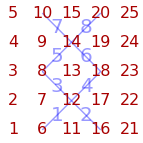

```mathematica
{vx,line}=GraphicPointLines[5,5,{{6,12},{16,12},{12,8},{12,18},{8,14},{18,14},{14,10},{14,20}}];
```

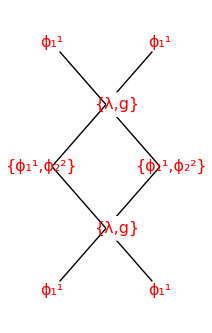

```mathematica
Graphics[{Thin,Black,Map[Line[#]&,line],
TextOver[ϕd[1],vx[[16]]],
TextOver[ϕd[1],vx[[6]]],
TextOver[ϕd[1],vx[[10]]],
TextOver[ϕd[1],vx[[20]]],
TextOver[{ϕd[1],ϕd[2]},vx[[8]]+{-.2,0}],
TextOver[{ϕd[1],ϕd[2]},vx[[18]]+{.2,0}],
TextOver[{λ,g},vx[[12]]+{.2,0}],
TextOver[{λ,g},vx[[14]]+{.2,0}]
}
]
```